```mathematica
ClearAll[m,k,T,h,v,vmin,nu]

vmin=Sqrt[(2 h nu)/m];

numerator=Integrate[v^3 Exp[-(m v^2)/(2 k T)] (1+0.3 (m v^2)/(k T)),{v,vmin,Infinity},Assumptions->{m>0,k>0,T>0,h>0,nu>0}];

denominator=Integrate[v^4 Exp[-(m v^2)/(2 k T)] (1+0.3 (m v^2)/(k T)),{v,0,Infinity},Assumptions->{m>0,k>0,T>0}];

ratio=Simplify[numerator/denominator,Assumptions->{m>0,k>0,T>0,h>0,nu>0}]
```

(0.106385 ⅇ^(-(h nu)/(k T)) (1.2 h^2 nu^2+4.4 h k nu T+4.4 k^2 T^2))/(m^2 ((k T)/m)^(5/2))

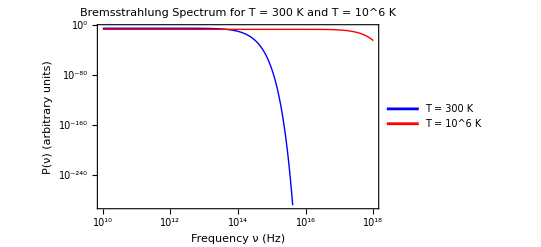

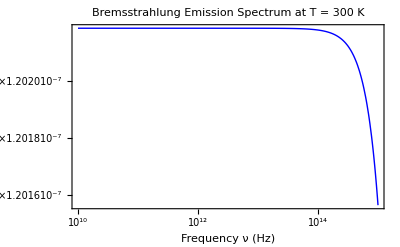

```mathematica
(*Define constants*)h=6.626*10^-34;       (*Planck constant in J*s*)
k=1.381*10^-23;       (*Boltzmann constant in J/K*)
m=9.109*10^-31;       (*Electron mass in kg*)

(*Define general function for P[nu,T]*)
P[nu_,T_]:=(0.106385*Exp[-(h*nu)/(k*T)]*(1.2*h^2*nu^2+4.4*h*k*nu*T+4.4*k^2*T^2))/(m^2*((k*T)/m)^(5/2))

(*Plot for both temperatures*)
Plot[{P[nu,300],P[nu,10^6]},{nu,10^10,10^18},PlotRange->All,PlotStyle->{{Thick,Blue},{Thick,Red}},Frame->True,FrameLabel->{"Frequency ν (Hz)","P(ν) (arbitrary units)"},PlotLabel->"Bremsstrahlung Spectrum for T = 300 K and T = 10^6 K",GridLines->Automatic,ScalingFunctions->{"Log10","Log10"},PlotLegends->{"T = 300 K","T = 10^6 K"}]
```